```mathematica
(*绝热消除中间能级*)
H1=1/2({{0, -Subscript[Ω, R] ⅇ^(ⅈ Subscript[ω, R] t), 0}, {-Subscript[Ω, R] ⅇ^(-ⅈ Subscript[ω, R] t), 2 Subscript[ω, 12], -Subscript[Ω, p] ⅇ^(ⅈ Subscript[ω, p] t)}, {0, -Subscript[Ω, p] ⅇ^(-ⅈ Subscript[ω, p] t), 2 Subscript[ω, 12]+2 Subscript[ω, 23]}});
U=({{1, 0, 0}, {0, ⅇ^(-ⅈ Subscript[ω, 12] t), 0}, {0, 0, ⅇ^(-ⅈ (Subscript[ω, 12]+Subscript[ω, 23] )t)}});
U†=({{1, 0, 0}, {0, ⅇ^(ⅈ Subscript[ω, 12] t), 0}, {0, 0, ⅇ^(ⅈ (Subscript[ω, 12]+Subscript[ω, 23] )t)}});
ⅈ*D[U†,t].U+U†.H1.U//MatrixForm//FullSimplify
```

(0 | -1/2 ⅇ^(-ⅈ t (ω_12-ω_R)) Ω_R | 0
-1/2 ⅇ^(ⅈ t (ω_12-ω_R)) Ω_R | 0 | -1/2 ⅇ^(-ⅈ t (ω_23-ω_p)) Ω_p
0 | -1/2 ⅇ^(ⅈ t (ω_23-ω_p)) Ω_p | 0)

```mathematica
H2=({{0, -1/2 ⅇ^(-ⅈ t (Subscript[ω, 12]-Subscript[ω, R])) Subscript[Ω, R], 0}, {-1/2 ⅇ^(ⅈ t (Subscript[ω, 12]-Subscript[ω, R])) Subscript[Ω, R], 0, -1/2 ⅇ^(-ⅈ t (Subscript[ω, 23]-Subscript[ω, p])) Subscript[Ω, p]}, {0, -1/2 ⅇ^(ⅈ t (Subscript[ω, 23]-Subscript[ω, p])) Subscript[Ω, p], 0}});
H3=-ⅈ H2.Integrate[H2,t]//FullSimplify//MatrixForm(*求有效H*)
```

(-Ω_R^2/(4 (ω_12-ω_R)) | 0 | (ⅇ^(-ⅈ t (ω_12+ω_23-ω_p-ω_R)) Ω_p Ω_R)/(4 (ω_23-ω_p))
0 | 1/4 (-Ω_p^2/(ω_23-ω_p)+Ω_R^2/(ω_12-ω_R)) | 0
-(ⅇ^(ⅈ t (ω_12+ω_23-ω_p-ω_R)) Ω_p Ω_R)/(4 (ω_12-ω_R)) | 0 | Ω_p^2/(4 ω_23-4 ω_p))

```mathematica
H4=({{-Subscript[Ω, R]^2/(4 (Subscript[ω, 12]-Subscript[ω, R])), (ⅇ^(-ⅈ t (Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R])) Subscript[Ω, p] Subscript[Ω, R])/(4 (Subscript[ω, 23]-Subscript[ω, p]))}, {-(ⅇ^(ⅈ t (Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R])) Subscript[Ω, p] Subscript[Ω, R])/(4 (Subscript[ω, 12]-Subscript[ω, R])), Subscript[Ω, p]^2/(4 Subscript[ω, 23]-4 Subscript[ω, p])}});
U=({{1, 0}, {0, ⅇ^(ⅈ (Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R])t)}});
U†=({{1, 0}, {0, ⅇ^(-ⅈ (Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R])t)}});
ⅈ*D[U†,t].U+U†.H4.U//MatrixForm//FullSimplify
```

(-Ω_R^2/(4 (ω_12-ω_R)) | (Ω_p Ω_R)/(4 ω_23-4 ω_p)
-(Ω_p Ω_R)/(4 (ω_12-ω_R)) | ω_12+ω_23-ω_p-ω_R+Ω_p^2/(4 ω_23-4 ω_p))

```mathematica
H5=({{-Subscript[Ω, R]^2/(4 (Subscript[ω, 12]-Subscript[ω, R])), (Subscript[Ω, p] Subscript[Ω, R])/(4 Subscript[ω, 23]-4 Subscript[ω, p]), 0}, {-(Subscript[Ω, p] Subscript[Ω, R])/(4 (Subscript[ω, 12]-Subscript[ω, R])), Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R]+Subscript[Ω, p]^2/(4 Subscript[ω, 23]-4 Subscript[ω, p]), -Subscript[Ω, m]/2 ⅇ^(ⅈ Subscript[ω, m] t)}, {0, -Subscript[Ω, m]/2 ⅇ^(-ⅈ Subscript[ω, m] t), Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, 34]}});
U=({{1, 0, 0}, {0, 1, 0}, {0, 0, ⅇ^(-ⅈ Subscript[ω, m] t)}});
U†=({{1, 0, 0}, {0, 1, 0}, {0, 0, ⅇ^(ⅈ Subscript[ω, m] t)}});
ⅈ*D[U†,t].U+U†.H5.U//MatrixForm//FullSimplify
```

```mathematica
({{-Subscript[Ω, R]^2/(4 (Subscript[ω, 12]-Subscript[ω, R])), (Subscript[Ω, p] Subscript[Ω, R])/(4 Subscript[ω, 23]-4 Subscript[ω, p]), 0}, {-(Subscript[Ω, p] Subscript[Ω, R])/(4 (Subscript[ω, 12]-Subscript[ω, R])), Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, p]-Subscript[ω, R]+Subscript[Ω, p]^2/(4 Subscript[ω, 23]-4 Subscript[ω, p]), -Subscript[Ω, m]/2}, {0, -Subscript[Ω, m]/2, Subscript[ω, 12]+Subscript[ω, 23]-Subscript[ω, 34]-Subscript[ω, m]}});
(*等效出三能级的H*)

ℋ=({{0, -Subscript[Ω, eff]/2, 0}, {-Subscript[Ω, eff]/2, Subscript[Δ, 13]+δ, -Subscript[Ω, m]/2}, {0, -Subscript[Ω, m]/2, δ-Subscript[Δ, m]}});
```

```mathematica
(*微扰到1阶*)

ℋ=({{0, -Subscript[Ω, eff]/2, 0}, {-Subscript[Ω, eff]/2, Subscript[Δ, 13]+δ, -Subscript[Ω, m]/2}, {0, -Subscript[Ω, m]/2, δ-Subscript[Δ, m]}});
ρ=({{ρ11[λ], ρ12[λ], ρ13[λ]}, {ρ21[λ], ρ22[λ], ρ23[λ]}, {ρ31[λ], ρ32[λ], ρ33[λ]}});
σ[i_,j_]:=Normal[SparseArray[{i,j}->1,3]];
ℒ12=Γ12/2( 2 σ[1,2].ρ.σ[2,1]-σ[2,2].ρ-ρ.σ[2,2]);
ℒ32=Γ32/2( 2σ[3,2].ρ .σ[2,3]-σ[2,2].ρ-ρ.σ[2,2]);
ℒ13=Γ13/2( 2 σ[1,3].ρ.σ[3,1]-σ[3,3].ρ-ρ.σ[3,3]);
dρ=-ⅈ(ℋ.ρ-ρ.ℋ)+ℒ12+ℒ32+ℒ13//FullSimplify//MatrixForm
```

(-1/2 ⅈ Ω_eff (ρ12[λ]-ρ21[λ])+Γ12 ρ22[λ]+Γ13 ρ33[λ] | -1/2 ⅈ (-ⅈ (Γ12+Γ32-2 ⅈ δ-2 ⅈ Δ_13) ρ12[λ]+Ω_m ρ13[λ]+Ω_eff (ρ11[λ]-ρ22[λ])) | -1/2 ⅈ (Ω_m ρ12[λ]+(-ⅈ Γ13-2 δ+2 Δ_m) ρ13[λ]-Ω_eff ρ23[λ])
1/2 ⅈ (ⅈ (Γ12+Γ32+2 ⅈ δ+2 ⅈ Δ_13) ρ21[λ]+Ω_eff (ρ11[λ]-ρ22[λ])+Ω_m ρ31[λ]) | 1/2 ⅈ (Ω_eff (ρ12[λ]-ρ21[λ])+2 ⅈ (Γ12+Γ32) ρ22[λ]+Ω_m (-ρ23[λ]+ρ32[λ])) | 1/2 ⅈ (Ω_eff ρ13[λ]+ⅈ (Γ12+Γ13+Γ32+2 ⅈ Δ_13+2 ⅈ Δ_m) ρ23[λ]+Ω_m (-ρ22[λ]+ρ33[λ]))
1/2 ⅈ (Ω_m ρ21[λ]+(ⅈ Γ13-2 δ+2 Δ_m) ρ31[λ]-Ω_eff ρ32[λ]) | 1/2 ⅈ (-Ω_eff ρ31[λ]+ⅈ (Γ12+Γ13+Γ32-2 ⅈ Δ_13-2 ⅈ Δ_m) ρ32[λ]+Ω_m (ρ22[λ]-ρ33[λ])) | Γ32 ρ22[λ]+1/2 ⅈ Ω_m (ρ23[λ]-ρ32[λ])-Γ13 ρ33[λ])

```mathematica
M=({{ρ11[λ], 1, -1/2 ⅈ Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+Γ12 ρ22[λ]+Γ13 ρ33[λ]}, {ρ12[λ], 2, -1/2 ⅈ (-ⅈ (Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) ρ12[λ]+Subscript[Ω, m] ρ13[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1]))}, {ρ13[λ], 3, -1/2 ⅈ (Subscript[Ω, m] ρ12[λ]+(-ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ13[λ]-Subscript[Ω, eff] ρ23[λ-1])}, {ρ21[λ], 4, 1/2 ⅈ (ⅈ (Γ12+Γ32+2 ⅈ δ+2 ⅈ Subscript[Δ, 13]) ρ21[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1])+Subscript[Ω, m] ρ31[λ])}, {ρ22[λ], 5, 1/2 ⅈ (Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+2 ⅈ (Γ12+Γ32) ρ22[λ]+Subscript[Ω, m] (-ρ23[λ]+ρ32[λ]))}, {ρ23[λ], 6, 1/2 ⅈ (Subscript[Ω, eff] ρ13[λ-1]+ⅈ (Γ12+Γ13+Γ32+2 ⅈ Subscript[Δ, 13]+2 ⅈ Subscript[Δ, m]) ρ23[λ]+Subscript[Ω, m] (-ρ22[λ]+ρ33[λ]))}, {ρ31[λ], 7, 1/2 ⅈ (Subscript[Ω, m] ρ21[λ]+(ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ31[λ]-Subscript[Ω, eff] ρ32[λ-1])}, {ρ32[λ], 8, 1/2 ⅈ (-Subscript[Ω, eff] ρ31[λ-1]+ⅈ (Γ12+Γ13+Γ32-2 ⅈ Subscript[Δ, 13]-2 ⅈ Subscript[Δ, m]) ρ32[λ]+Subscript[Ω, m] (ρ22[λ]-ρ33[λ]))}, {ρ33[λ], 9, Γ32 ρ22[λ]+1/2 ⅈ Subscript[Ω, m] (ρ23[λ]-ρ32[λ])-Γ13 ρ33[λ]}});
```

```mathematica
(*000000000*)
λ=0;
Subscript[Ω, eff] =0;
M=({{ρ11[λ], 1, -1/2 ⅈ Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+Γ12 ρ22[λ]+Γ13 ρ33[λ]}, {ρ12[λ], 2, -1/2 ⅈ (-ⅈ (Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) ρ12[λ]+Subscript[Ω, m] ρ13[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1]))}, {ρ13[λ], 3, -1/2 ⅈ (Subscript[Ω, m] ρ12[λ]+(-ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ13[λ]-Subscript[Ω, eff] ρ23[λ-1])}, {ρ21[λ], 4, 1/2 ⅈ (ⅈ (Γ12+Γ32+2 ⅈ δ+2 ⅈ Subscript[Δ, 13]) ρ21[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1])+Subscript[Ω, m] ρ31[λ])}, {ρ22[λ], 5, 1/2 ⅈ (Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+2 ⅈ (Γ12+Γ32) ρ22[λ]+Subscript[Ω, m] (-ρ23[λ]+ρ32[λ]))}, {ρ23[λ], 6, 1/2 ⅈ (Subscript[Ω, eff] ρ13[λ-1]+ⅈ (Γ12+Γ13+Γ32+2 ⅈ Subscript[Δ, 13]+2 ⅈ Subscript[Δ, m]) ρ23[λ]+Subscript[Ω, m] (-ρ22[λ]+ρ33[λ]))}, {ρ31[λ], 7, 1/2 ⅈ (Subscript[Ω, m] ρ21[λ]+(ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ31[λ]-Subscript[Ω, eff] ρ32[λ-1])}, {ρ32[λ], 8, 1/2 ⅈ (-Subscript[Ω, eff] ρ31[λ-1]+ⅈ (Γ12+Γ13+Γ32-2 ⅈ Subscript[Δ, 13]-2 ⅈ Subscript[Δ, m]) ρ32[λ]+Subscript[Ω, m] (ρ22[λ]-ρ33[λ]))}, {ρ33[λ], 9, Γ32 ρ22[λ]+1/2 ⅈ Subscript[Ω, m] (ρ23[λ]-ρ32[λ])-Γ13 ρ33[λ]}});
equs={M⟦5,3⟧==0,M⟦2,3⟧==0,M⟦3,3⟧==0,M⟦4,3⟧==0,M⟦6,3⟧==0,M⟦7,3⟧==0,M⟦8,3⟧==0,M⟦9,3⟧==0,ρ11[λ]+ρ22[λ]+ρ33[λ]==1};
vars={ρ11[λ],ρ12[λ],ρ13[λ],ρ21[λ],ρ22[λ],ρ23[λ],ρ31[λ],ρ32[λ],ρ33[λ]};
sol=Solve[equs,vars]//FullSimplify//Flatten
```

{ρ11[0]→1,ρ12[0]→0,ρ13[0]→0,ρ21[0]→0,ρ22[0]→0,ρ23[0]→0,ρ31[0]→0,ρ32[0]→0,ρ33[0]→0}

```mathematica
(*111111*)

λ=1;
ρ11[0]=1;
ρ12[0]=0;
ρ13[0]=0;
ρ21[0]=0;
ρ22[0]=0;
ρ23[0]=0;
ρ31[0]=0;
ρ32[0]=0;
ρ33[0]=0;
M=({{ρ11[λ], 1, -1/2 ⅈ Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+Γ12 ρ22[λ]+Γ13 ρ33[λ]}, {ρ12[λ], 2, -1/2 ⅈ (-ⅈ (Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) ρ12[λ]+Subscript[Ω, m] ρ13[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1]))}, {ρ13[λ], 3, -1/2 ⅈ (Subscript[Ω, m] ρ12[λ]+(-ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ13[λ]-Subscript[Ω, eff] ρ23[λ-1])}, {ρ21[λ], 4, 1/2 ⅈ (ⅈ (Γ12+Γ32+2 ⅈ δ+2 ⅈ Subscript[Δ, 13]) ρ21[λ]+Subscript[Ω, eff] (ρ11[λ-1]-ρ22[λ-1])+Subscript[Ω, m] ρ31[λ])}, {ρ22[λ], 5, 1/2 ⅈ (Subscript[Ω, eff] (ρ12[λ-1]-ρ21[λ-1])+2 ⅈ (Γ12+Γ32) ρ22[λ]+Subscript[Ω, m] (-ρ23[λ]+ρ32[λ]))}, {ρ23[λ], 6, 1/2 ⅈ (Subscript[Ω, eff] ρ13[λ-1]+ⅈ (Γ12+Γ13+Γ32+2 ⅈ Subscript[Δ, 13]+2 ⅈ Subscript[Δ, m]) ρ23[λ]+Subscript[Ω, m] (-ρ22[λ]+ρ33[λ]))}, {ρ31[λ], 7, 1/2 ⅈ (Subscript[Ω, m] ρ21[λ]+(ⅈ Γ13-2 δ+2 Subscript[Δ, m]) ρ31[λ]-Subscript[Ω, eff] ρ32[λ-1])}, {ρ32[λ], 8, 1/2 ⅈ (-Subscript[Ω, eff] ρ31[λ-1]+ⅈ (Γ12+Γ13+Γ32-2 ⅈ Subscript[Δ, 13]-2 ⅈ Subscript[Δ, m]) ρ32[λ]+Subscript[Ω, m] (ρ22[λ]-ρ33[λ]))}, {ρ33[λ], 9, Γ32 ρ22[λ]+1/2 ⅈ Subscript[Ω, m] (ρ23[λ]-ρ32[λ])-Γ13 ρ33[λ]}});
equs={M⟦5,3⟧==0,M⟦2,3⟧==0,M⟦3,3⟧==0,M⟦4,3⟧==0,M⟦6,3⟧==0,M⟦7,3⟧==0,M⟦8,3⟧==0,M⟦9,3⟧==0,M⟦1,3⟧==0,ρ11[λ]+ρ22[λ]+ρ33[λ]==1};
vars={ρ11[λ],ρ12[λ],ρ13[λ],ρ21[λ],ρ22[λ],ρ23[λ],ρ31[λ],ρ32[λ],ρ33[λ]};
Solve[equs,vars]//FullSimplify//Flatten
```

{ρ11[1]→1,ρ12[1]→((Γ13-2 ⅈ δ+2 ⅈ Δ_m) Ω_eff)/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Δ_13) (ⅈ Γ13+2 δ-2 Δ_m)+ⅈ Ω_m^2),ρ13[1]→-(Ω_eff Ω_m)/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Δ_13) (Γ13-2 ⅈ δ+2 ⅈ Δ_m)+Ω_m^2),ρ21[1]→((Γ13+2 ⅈ δ-2 ⅈ Δ_m) Ω_eff)/((Γ12+Γ32+2 ⅈ δ+2 ⅈ Δ_13) (-ⅈ Γ13+2 δ-2 Δ_m)-ⅈ Ω_m^2),ρ22[1]→0,ρ23[1]→0,ρ31[1]→-(Ω_eff Ω_m)/((Γ12+Γ32+2 ⅈ δ+2 ⅈ Δ_13) (Γ13+2 ⅈ δ-2 ⅈ Δ_m)+Ω_m^2),ρ32[1]→0,ρ33[1]→0}

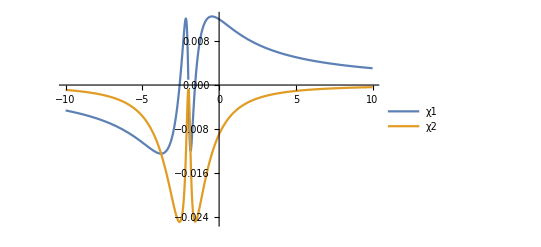

```mathematica
(*用1阶结果去计算*)
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.3;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Plot[{χ1,χ2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"χ1","χ2"},Right]]
```

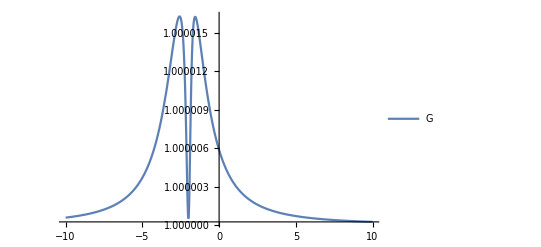

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.3;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);

Plot[{G},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"G"},Right]]
```

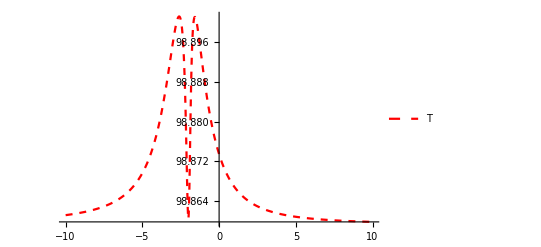

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.5;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);

Τ=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Plot[Τ,{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Τ"},Right],PlotStyle->{Red,Dashed}]
```

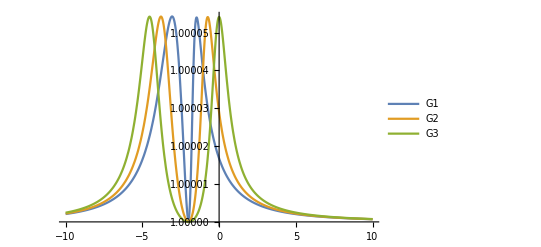

```mathematica
(*Subscript[改变Ω, m]*)

ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.5;
Subscript[Ω, R]=2;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[Ω, m]=3;
G2=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[Ω, m]=4.5;
G3=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ3=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Plot[{G1,G2,G3},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"G1","G2","G3"},Right]]
```

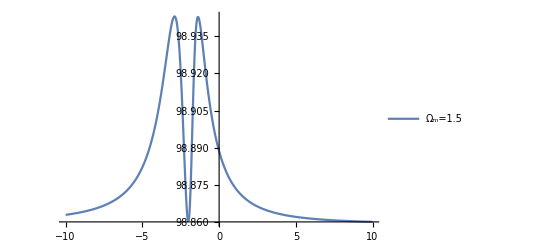

```mathematica
(*透射谱*)
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);

Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Plot[{Τ1},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_m=1.5"},Right]]
```

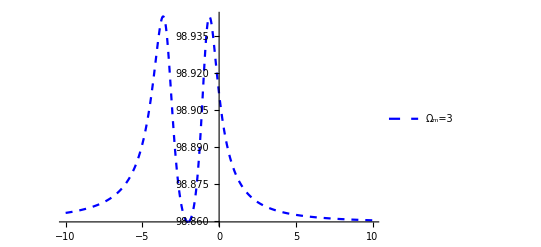

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=3;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);

Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_m=3"},Right],PlotStyle->{Blue,Dashed}]
```

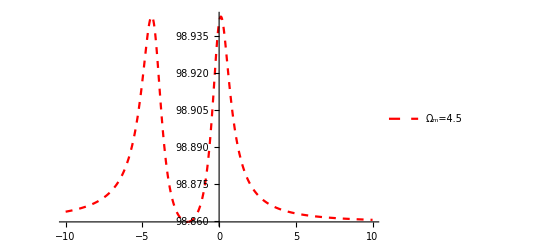

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=4.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);

Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_m=4.5"},Right],PlotStyle->{Red,Dashed}]
```

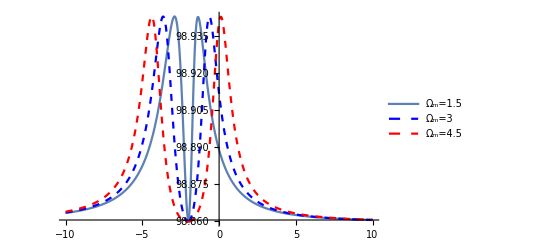

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

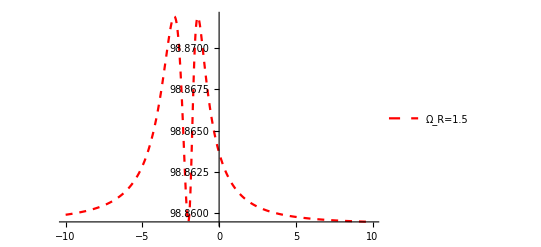

```mathematica
(*Subscript[改变Ω, R]*)

ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=1.5;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ1},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_R=1.5"},Right],PlotStyle->{Red,Dashed}]
```

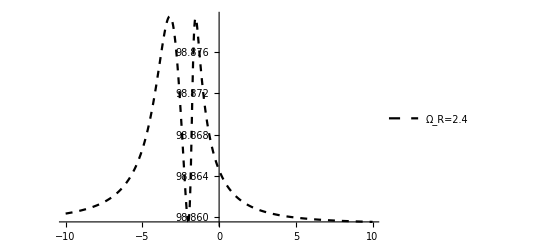

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=2.4;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_R=2.4"},Right],PlotStyle->{Black,Dashed}]
```

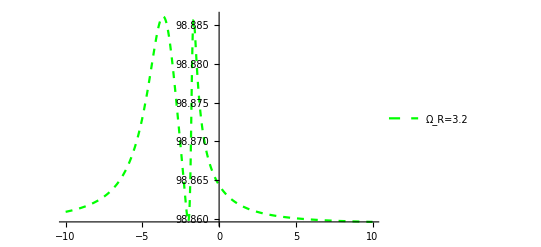

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=3.2;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ3=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ3},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Ω_R=3.2"},Right],PlotStyle->{Green,Dashed}]
```

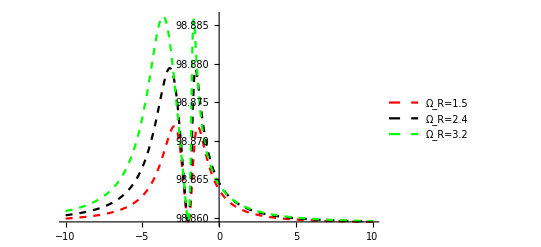

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

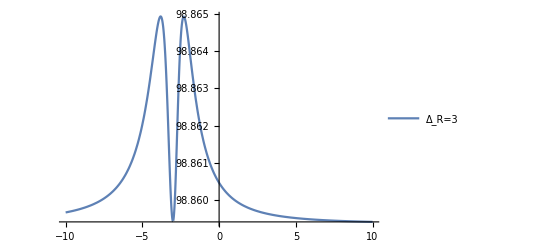

```mathematica
(*Subscript[改变Δ, R]*)

ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=3;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ1},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Δ_R=3"},Right]]
```

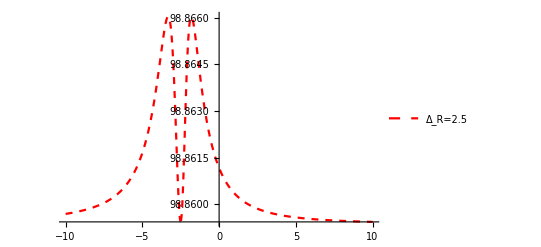

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2.5;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Δ_R=2.5"},Right],PlotStyle->{Red,Dashed}]
```

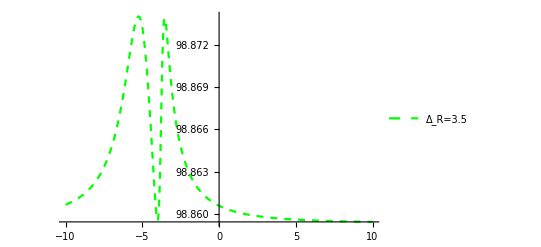

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=4;
Subscript[Ω, p]=0.1;
Subscript[Ω, R]=3.5;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ3=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ3},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Δ_R=3.5"},Right],PlotStyle->{Green,Dashed}]
```

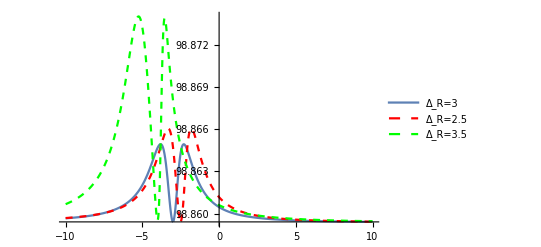

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

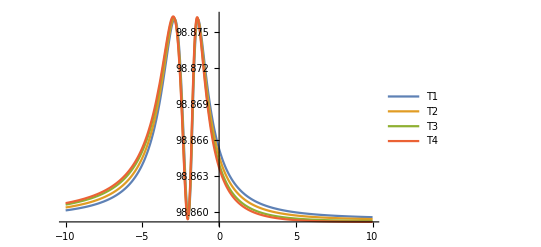

```mathematica
(*Subscript[改变ℓ, a]*)

ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=3;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=1;
Subscript[Ω, R]=1;
Subscript[Ω, m]=1.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.01;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[ℓ, a]=0.03;
G2=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[ℓ, a]=0.05;
G3=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ3=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[ℓ, a]=0.06;
G4=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ4=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{Τ1,Τ2,Τ3,Τ4},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"Τ1","Τ2","Τ3","Τ4"},Right]]
```

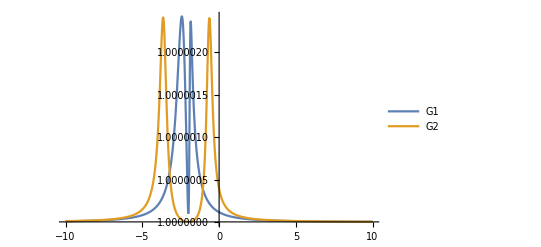

```mathematica
ρ12[1]=((Γ13-2 ⅈ δ+2 ⅈ Subscript[Δ, m]) Subscript[Ω, eff])/((Γ12+Γ32-2 ⅈ δ-2 ⅈ Subscript[Δ, 13]) (ⅈ Γ13+2 δ-2 Subscript[Δ, m])+ⅈ Subscript[Ω, m]^2);
Subscript[Ω, eff]=(Subscript[Ω, p]*Subscript[Ω, R])/(2*Subscript[Δ, R]);
δ=Subscript[Δ, p]+Subscript[Δ, R];
Subscript[Δ, 13]=(Subscript[Ω, p]*Subscript[Ω, p]+Subscript[Ω, R]*Subscript[Ω, R])/(4*Subscript[Δ, R]);

χ1=Re[ρ12[1]];
χ2=Im[ρ12[1]];
Γ12=1;
Γ32=0.01;
Γ13=0.01;
Subscript[Δ, m]=0;
Subscript[Δ, R]=2;
Subscript[Ω, p]=0.01;
Subscript[Ω, R]=1.5;
Subscript[Ω, m]=0.5;
r=0.98;
t=0.199;
Subscript[ℓ, a]=0.05;
L=0.369;
Subscript[λ, p]=480;
𝒦=ⅇ^(-(Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
G1=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ1=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);
Subscript[Ω, m]=3;
G2=ⅇ^(-(2*3.14*Subscript[ℓ, a]*χ2)/Subscript[λ, p]);
Τ2=t^2/(1+r^2*𝒦^2-2*r*𝒦*Cos[(L+Subscript[ℓ, a]*χ1)/Subscript[λ, p]]);

Plot[{G1,G2},{Subscript[Δ, p],-10,10},PlotRange->All,PlotLegends->Placed[{"G1","G2"},Right]]
```

```mathematica
Eigensystem[({{Δ/2, Subscript[Ω, R]/2}, {Subscript[Ω, R]/2, -Δ/2}})]//FullSimplify
```

{{-1/2 √(Δ^2+Ω_R^2),1/2 √(Δ^2+Ω_R^2)},{{(Δ-√(Δ^2+Ω_R^2))/Ω_R,1},{(Δ+√(Δ^2+Ω_R^2))/Ω_R,1}}}

```mathematica
Eigensystem[({{0, -Subscript[Ω, R]}, {-Subscript[Ω, R], Δ}})]//FullSimplify
```

{{1/2 (Δ-√(Δ^2+4 Ω_R^2)),1/2 (Δ+√(Δ^2+4 Ω_R^2))},{{(Δ+√(Δ^2+4 Ω_R^2))/(2 Ω_R),1},{(Δ-√(Δ^2+4 Ω_R^2))/(2 Ω_R),1}}}

```mathematica
Normalize[{(Δ+√(Δ^2+4 Subscript[Ω, R]^2))/(2 Subscript[Ω, R]),1}]//FullSimplify
```

```mathematica
{(Δ+√(Δ^2+4 Subscript[Ω, R]^2))/(√(4+Abs[(Δ+√(Δ^2+4 Subscript[Ω, R]^2))/Subscript[Ω, R]]^2) Subscript[Ω, R]),2/(√(4+Abs[(Δ+√(Δ^2+4 Subscript[Ω, R]^2))/Subscript[Ω, R]]^2))}
```

```mathematica
H2=({{0, -1/2 ⅇ^(-ⅈ t (Subscript[ω, 12]-Subscript[ω, R])) Subscript[Ω, R], 0}, {-1/2 ⅇ^(ⅈ t (Subscript[ω, 12]-Subscript[ω, R])) Subscript[Ω, R], 0, -1/2 ⅇ^(-ⅈ t (Subscript[ω, 23]-Subscript[ω, p])) Subscript[Ω, p]}, {0, -1/2 ⅇ^(ⅈ t (Subscript[ω, 23]-Subscript[ω, p])) Subscript[Ω, p], 0}});
H3=-H2.Integrate[Integrate[H2,t],t]//FullSimplify//MatrixForm
```

(Ω_R^2/(4 (ω_12-ω_R)^2) | 0 | (ⅇ^(-ⅈ t (ω_12+ω_23-ω_p-ω_R)) Ω_p Ω_R)/(4 (ω_23-ω_p)^2)
0 | 1/4 (Ω_p^2/(ω_23-ω_p)^2+Ω_R^2/(ω_12-ω_R)^2) | 0
(ⅇ^(ⅈ t (ω_12+ω_23-ω_p-ω_R)) Ω_p Ω_R)/(4 (ω_12-ω_R)^2) | 0 | Ω_p^2/(4 (ω_23-ω_p)^2))